```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
repl={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,χ,ϕ,θp,ϕp,kp,vter,vter,cq,vf,B,μ,chi,fac} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && βtra>0 && βter>0 && cq>=0 && vf>0 && B>0;
```

## band plots

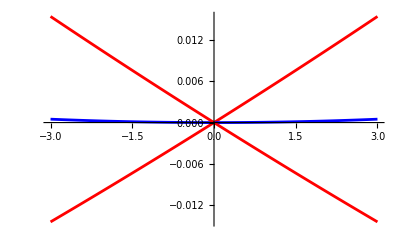

```mathematica
cqval=0.011;vfval=0.005;
Plot[{vfval k( 1+cqval k),vfval cqval k^2,vfval k(- 1+cqval k)},{k,-3,3},PlotStyle->{Red,Blue,Red}]
```

## Computing W_kk'

```mathematica
sx=({{0, 1/(√2), 0}, {1/(√2), 0, 1/(√2)}, {0, 1/(√2), 0}});sy=1/(√2)({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}});sz=({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
(*********)
Clear[ham];
repl={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ham[χ_]= χ(kx sx+ky sy+ kz sz)+ cq k^2 IdentityMatrix[3];
Print["χ=1"];
FullSimplify[FullSimplify[Eigensystem[ham[1]],ass]/.repl,ass]
Print["χ=-1"];
FullSimplify[FullSimplify[Eigensystem[ham[-1]],ass]/.repl,ass]
(* -Graphics- *)
```

χ=1

{{cq k^2,k (-1+cq k),k (1+cq k)},{{-ⅇ^(-2 ⅈ ϕ),√2 ⅇ^(-ⅈ ϕ) Cot[θ],1},{ⅇ^(-2 ⅈ ϕ) Tan[θ/2]^2,(√2 ⅇ^(-ⅈ ϕ) (-1+Cos[θ]))/Sin[θ],1},{ⅇ^(-2 ⅈ ϕ) Cot[θ/2]^2,√2 ⅇ^(-ⅈ ϕ) Cot[θ/2],1}}}

χ=-1

{{cq k^2,k (-1+cq k),k (1+cq k)},{{-ⅇ^(-2 ⅈ ϕ),√2 ⅇ^(-ⅈ ϕ) Cot[θ],1},{ⅇ^(-2 ⅈ ϕ) Cot[θ/2]^2,√2 ⅇ^(-ⅈ ϕ) Cot[θ/2],1},{ⅇ^(-2 ⅈ ϕ) Tan[θ/2]^2,(√2 ⅇ^(-ⅈ ϕ) (-1+Cos[θ]))/Sin[θ],1}}}

```mathematica
(* χ=1, s=1 *) Sin[θ/2]^2{ⅇ^(-2 ⅈ ϕ) Cot[θ/2]^2,√2 ⅇ^(-ⅈ ϕ) Cot[θ/2],1}=={ⅇ^(-2 ⅈ ϕ)Cos[θ/2]^2,(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Sin[θ/2]^2}//FullSimplify
(* χ=1 or χ=-1, s=0 *) Sin[θ]{-ⅇ^(-2 ⅈ ϕ),√2 ⅇ^(-ⅈ ϕ) Cot[θ],1}//FullSimplify

(* χ=-1, s=1 *)  Cos[θ/2]^2{ⅇ^(-2 ⅈ ϕ) Tan[θ/2]^2,(√2 ⅇ^(-ⅈ ϕ) (-1+Cos[θ]))/Sin[θ],1}=={ⅇ^(-2 ⅈ ϕ) Sin[θ/2]^2,-(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ/2]^2}//FullSimplify
```

True

{-ⅇ^(-2 ⅈ ϕ) Sin[θ],√2 ⅇ^(-ⅈ ϕ) Cos[θ],Sin[θ]}

True

```mathematica
TeXForm[{(-ⅇ^(-2 ⅈ ϕ) Sin[θ])/(√2), ⅇ^(-ⅈ ϕ) Cos[θ],Sin[θ]/(√2)}]
```

```mathematica
(* checking normalization*) Clear[vec1,vec1dag];
vec1[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ)Cos[θ/2]^2,(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Sin[θ/2]^2}//FullSimplify;
vec1dag[θ_,ϕ_]={ⅇ^(2 ⅈ ϕ)Cos[θ/2]^2,(ⅇ^(ⅈ ϕ) Sin[θ])/(√2),Sin[θ/2]^2}//FullSimplify;
FullSimplify[vec1dag[θ,ϕ].vec1[θ,ϕ],ass]
Clear[vec2,vec2dag];
vec2[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ) Sin[θ/2]^2,-(ⅇ^(-ⅈ ϕ) Sin[θ])/(√2),Cos[θ/2]^2}//FullSimplify;
vec2dag[θ_,ϕ_]={ⅇ^(2 ⅈ ϕ) Sin[θ/2]^2,-(ⅇ^(ⅈ ϕ) Sin[θ])/(√2),Cos[θ/2]^2}//FullSimplify;
FullSimplify[vec2dag[θ,ϕ].vec2[θ,ϕ],ass]

Clear[vec0,vec0dag];
vec0[θ_,ϕ_]=1/(√2){-ⅇ^(-2 ⅈ ϕ) Sin[θ],√2 ⅇ^(-ⅈ ϕ) Cos[θ],Sin[θ]}//FullSimplify;
vec0dag[θ_,ϕ_]=1/(√2){-ⅇ^(2 ⅈ ϕ) Sin[θ],√2 ⅇ^(ⅈ ϕ) Cos[θ],Sin[θ]}//FullSimplify;
FullSimplify[vec0dag[θ,ϕ].vec0[θ,ϕ],ass]
```

1

1

1

```mathematica
Clear[vec1,vec1dag,vec2,vec2dag,vec0,vec0dag];
vec1[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ)cos[θ/2]^2,(ⅇ^(-ⅈ ϕ) sin[θ])/(√2),sin[θ/2]^2}//FullSimplify;vec2[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ) sin[θ/2]^2,-(ⅇ^(-ⅈ ϕ) sin[θ])/(√2),cos[θ/2]^2}//FullSimplify;
vec0[θ_,ϕ_]=1/(√2){-ⅇ^(-2 ⅈ ϕ) sin[θ],√2 ⅇ^(-ⅈ ϕ) cos[θ],sin[θ]}//FullSimplify;
(* conjugates *)
vec1dag[θ_,ϕ_]={ⅇ^(2 ⅈ ϕ)cos[θ/2]^2,(ⅇ^(ⅈ ϕ) sin[θ])/(√2),sin[θ/2]^2}//FullSimplify;
vec2dag[θ_,ϕ_]={ⅇ^(2 ⅈ ϕ) sin[θ/2]^2,-(ⅇ^(ⅈ ϕ) sin[θ])/(√2),cos[θ/2]^2}//FullSimplify;
vec0dag[θ_,ϕ_]=1/(√2){-ⅇ^(2 ⅈ ϕ) sin[θ],√2 ⅇ^(ⅈ ϕ) cos[θ],sin[θ]}//FullSimplify;

tra11 (*or βm1m1*)FullSimplify[Integrate[((vec1dag[θ,ϕ].vec1[θp,ϕp])(vec1dag[θp,ϕp].vec1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
ter11 FullSimplify[Integrate[((vec1dag[θ,ϕ].vec2[θp,ϕp])(vec2dag[θp,ϕp].vec1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
ter00 (* or tra00 *) FullSimplify[Integrate[((vec0dag[θ,ϕ].vec0[θp,ϕp])(vec0dag[θp,ϕp].vec0[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
tra10 FullSimplify[Integrate[((vec1dag[θ,ϕ].vec0[θp,ϕp])(vec0dag[θp,ϕp].vec1[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
tra20 FullSimplify[Integrate[((vec2dag[θ,ϕ].vec0[θp,ϕp])(vec0dag[θp,ϕp].vec2[θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
```

tra11 (cos[θ/2]^4 cos[θp/2]^4+sin[θ/2]^4 sin[θp/2]^4+1/4 sin[θ]^2 sin[θp]^2)

ter11 (cos[θp/2]^4 sin[θ/2]^4+cos[θ/2]^4 sin[θp/2]^4+1/4 sin[θ]^2 sin[θp]^2)

ter00 (cos[θ]^2 cos[θp]^2+1/2 sin[θ]^2 sin[θp]^2)

1/2 tra10 (cos[θp]^2 sin[θ]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2)

1/2 tra20 (cos[θp]^2 sin[θ]^2+(cos[θ/2]^4+sin[θ/2]^4) sin[θp]^2)

```mathematica
TeXForm[Cos[θ']^2 Sin[θ]^2+(Cos[θ/2]^4+Sin[θ/2]^4) Sin[θ']^2]
```

\sin ^2\left(\theta '\right) \left(\sin ^4\left(\frac{\theta }{2}\right)+\cos ^4\left(\frac{\theta }{2}\right)\right)+\sin ^2(\theta
   ) \cos ^2\left(\theta '\right)

```mathematica
(* vec1[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ)cos[θ/2]^2,(ⅇ^(-ⅈ ϕ) sin[θ])/(√2),sin[θ/2]^2}//FullSimplify;vec2[θ_,ϕ_]={ⅇ^(-2 ⅈ ϕ) sin[θ/2]^2,-(ⅇ^(-ⅈ ϕ) sin[θ])/(√2),cos[θ/2]^2}//FullSimplify;
vec0[θ_,ϕ_]=1/(√2){-ⅇ^(-2 ⅈ ϕ) sin[θ],√2 ⅇ^(-ⅈ ϕ) cos[θ],sin[θ]}//FullSimplify; *)
```

## Matrix forms

```mathematica
Clear[G];G[χ_, η_,sχ_,sη_]=(*2 flat bands: ter00 (cos[θ]^2 cos[θp]^2+1/2 sin[θ]^2 sin[θp]^2*)KroneckerDelta[sχ ,0]KroneckerDelta[sη ,0](ct2 ctp2+1/2 st2 stp2)+
(* flat band & cond. band *)KroneckerDelta[sχ ,0]KroneckerDelta[sη ,1](ct2 stp2+st2 (ctp4 +stp4))/2+(*cond. band & flat band*)KroneckerDelta[sχ ,1]KroneckerDelta[sη ,0](ctp2 st2+stp2 (ct4 +st4))/2+KroneckerDelta[χ ,η]KroneckerDelta[sχ ,1]KroneckerDelta[sη ,1](ct4 ctp4+st4 stp4+(st2 stp2)/4)+KroneckerDelta[-χ, η]KroneckerDelta[sχ ,1]KroneckerDelta[sη ,1](st4 ctp4+ct4 stp4+(st2 stp2)/4);
G[1,-1,0,1]
```

1/2 (ct2 stp2+st2 (ctp4+stp4))

```mathematica
TeXForm[Cos[θ/2]^4]
```

\cos ^4\left(\frac{\theta }{2}\right)

```mathematica
Clear[eq,Λ11byτ,Λ21byτ,Λ10byτ,Λ20byτ,lhs1,lhs2,lhs3,lhs4,rhs1,rhs2,rhs3,rhs4,λ,a,b,h11,h21,h10,c11,eqn1,eqn2,eqn3,eqn4,eqn5,eqn6,eqn7,eqn8,eqn9,eqn10,eqn11];
Λ11byτ=(-h11+a11 ct4(* Cos[θ/2]^4 *)+b11 st4(* Sin[θ/2]^4 *)+c11 st2(* Sin[θ]^2*));
Λ21byτ=(-h21+a21 ct4+b21 st4+c21 st2);
Λ10byτ=(-h10+c10 st2(* Sin[θ]^2*)+d10 ct2(* Cos[θ]^2*));
Λ20byτ=(-h10+c20 st2+d20 ct2);

(* -Graphics- ; -Graphics-*)
lhs1=a11 ct4+b11 st4+c11 st2;     lhs2=a21 ct4+b21 st4+c21 st2;
lhs3=c10 st2+d10 ct2;       lhs4=c20 st2+d20 ct2;

rhs1=tra11 intθpf11 G[1,1,1,1](-h11+a11 ctp4+b11 stp4+c11 stp2)+tra10 intθpf10 G[1,1,1,0](-h10+c10 stp2+d10 ctp2)+ter11 intθpf21 G[1,-1,1,1](-h21+a21 ctp4+b21 stp4+c21 stp2)+ter10 intθpf20 G[1,-1,1,0](-h20+c20 stp2+d20 ctp2);

rhs2=tra11 intθpf21 G[-1,-1,1,1](-h21+a21 ctp4+b21 stp4+c21 stp2)+tra10 intθpf20 G[-1,-1,1,0](-h20+c20 stp2+d20 ctp2)+ter11 intθpf11 G[-1,1,1,1](-h11+a11 ctp4+b11 stp4+c11 stp2)+ter10 intθpf10 G[-1,1,1,0](-h10+c10 stp2+d10 ctp2);

rhs3=tra00 intθpf10 G[1,1,0,0](-h10+c10 stp2+d10 ctp2)+tra10 intθpf11 G[1,1,0,1](-h11+a11 ctp4+b11 stp4+c11 stp2)+ter00 intθpf20 G[1,-1,0,0](-h20+c20 stp2+d20 ctp2)+ter10 intθpf21 G[1,-1,0,1](-h21+a21 ctp4+b21 stp4+c21 stp2)//FullSimplify;

rhs4=tra00 intθpf20 G[-1,-1,0,0](-h20+c20 stp2+d20 ctp2)+tra10 intθpf21 G[-1,-1,0,1](-h21+a21 ctp4+b21 stp4+c21 stp2)+ter00 intθpf10 G[-1,1,0,0](-h10+c10 stp2+d10 ctp2)+ter10 intθpf11 G[-1,1,0,1](-h11+a11 ctp4+b11 stp4+c11 stp2)//FullSimplify;

eq=lhs1-rhs1;
eqn1=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0}]//FullSimplify;
eqn2=SeriesCoefficient[eq,{ct4,0,1},{st4,0,0},{st2,0,0}]//FullSimplify;
eqn3=SeriesCoefficient[eq,{ct4,0,0},{st4,0,1},{st2,0,0}]//FullSimplify;
eqn4=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1}]//FullSimplify;
eq==eqn1+eqn2 ct4+eqn3 st4+ eqn4 st2//FullSimplify

eq=lhs2-rhs2;
eqn5=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0}]//FullSimplify;
eqn6=SeriesCoefficient[eq,{ct4,0,1},{st4,0,0},{st2,0,0}]//FullSimplify;
eqn7=SeriesCoefficient[eq,{ct4,0,0},{st4,0,1},{st2,0,0}]//FullSimplify;
eqn8=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1}]//FullSimplify;
eq==eqn5+eqn6 ct4+eqn7 st4+ eqn8 st2//FullSimplify

eq=lhs3-rhs3;
eqn9=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0},{ct2,0,0}]//FullSimplify;
eqn10=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1},{ct2,0,0}]//FullSimplify;
eqn11=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0},{ct2,0,1}]//FullSimplify;
eq==eqn9+ eqn10 st2+ eqn11 ct2//FullSimplify

eq=lhs4-rhs4;
eqn12=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0},{ct2,0,0}]//FullSimplify;
eqn13=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,1},{ct2,0,0}]//FullSimplify;
eqn14=SeriesCoefficient[eq,{ct4,0,0},{st4,0,0},{st2,0,0},{ct2,0,1}]//FullSimplify;
eq==eqn12+ eqn13 st2+ eqn14 ct2//FullSimplify

(* Print["charge consvn:"];*)
intθf11 Λ11byτ+intθf21 Λ21byτ+intθf10 Λ10byτ +intθf20 Λ20byτ
```

True

True

True

«1 more identical outputs»

intθf10 (ct2 d10-h10+c10 st2)+intθf20 (ct2 d20-h10+c20 st2)+intθf11 (a11 ct4-h11+c11 st2+b11 st4)+intθf21 (a21 ct4-h21+c21 st2+b21 st4)

```mathematica
Clear[arr,array,array1,cmat];arr=CoefficientArrays[{eqn2==0,eqn3==0,eqn4==0,eqn6==0,eqn7==0,eqn8==0,eqn10==0,eqn11==0,eqn13==0,eqn14==0},{a11,b11,c11,a21,b21,c21,c10,d10,c20,d20}];
array=Normal[arr]//Simplify;
cmat=array[[2]]//Simplify;
rep={intθpf11->af11,intθpf21->af21,intθpf10->af10,intθpf20->af20,ctp4->ct4,stp4->st4,stp2->st2,ctp2->ct2};
cmat=Expand[cmat/.rep];
array[[1]]=Expand[array[[1]]/.rep];
rep1={af10 ct2^3->ct2ct2ct210,af20 ct2^3->ct2ct2ct220,af10 ct2^2 st2->ct2ct2at210,af20 ct2^2 st2->ct2ct2at220,af10 ct2 st2->ct2st210,af10 ct2^2->ct2ct210,af20 ct2 st2->ct2st220,af20 ct2^2->ct2ct220,af20 st2^2->st2st220,af10 st2^2->st2st210,af20 h20 st2->hst220,af10 h10 st2->hst210,af10 ct2 h10->hct210,af20 ct2 h20->hct220,
(***********)af20 ct2->ct220,af10 ct2->ct210, af10->zero10,af20->zero20,(**************************)af21 h21 st2->hst221,af21 h21 st4->hst421,af11 ct4 h11->hct411,af21 ct4 h21->hct421,af11 h11 st4->hst411,af11 h11 st2->hst211,af10 h10->hzero10,af20 h20->hzero20,(**************)af11 ct4 st4->ct4st411,af11 ct4 st2->ct4st211,af11 ct4->ct411,af11 st4 st2->st4st211, af11 st4->st411,af11 st2->st211,af11 (ct4-st2+st4)->ct411-st211+st411,af11 ct4^2->ct4ct411,af11 st4^2->st4st411,af11 st2^2->st2st211,(**********)af21 ct4 st4->ct4st421,af21 ct4 st2->ct4st221,af21 ct4->ct421,af21 st4 st2->st4st221, af21 st4->st421,af21 st2->st221,af21 (ct4-st2+st4)->ct421-st221+st421,af21 ct4^2->ct4ct421,af21 st4^2->st4st421,af21 st2^2->st2st221,(********)af10 st2->st210,af10 st2^2->st2st210,af20 st2 ->st220,af20 st2^2->st2st220,af10->zero10,af20->zero20};
MatrixForm[cmat/.rep1]//FullSimplify
MatrixForm[array[[1]]/.rep1]//FullSimplify
MatrixRank[cmat]
```

(1-ct4ct411 tra11 | -ct4st411 tra11 | -ct4st211 tra11 | -ct4st421 ter11 | -st4st421 ter11 | -st4st221 ter11 | -(st2st210 tra10)/2 | -(ct2st210 tra10)/2 | -(st2st220 ter10)/2 | -(ct2st220 ter10)/2
-ct4st411 tra11 | 1-st4st411 tra11 | -st4st211 tra11 | -ct4ct421 ter11 | -ct4st421 ter11 | -ct4st221 ter11 | -(st2st210 tra10)/2 | -(ct2st210 tra10)/2 | -(st2st220 ter10)/2 | -(ct2st220 ter10)/2
-(ct4st211 tra11)/4 | -(st4st211 tra11)/4 | 1-(st2st211 tra11)/4 | -(ct4st221 ter11)/4 | -(st4st221 ter11)/4 | -(st2st221 ter11)/4 | -(ct2st210 tra10)/2 | -(ct2ct210 tra10)/2 | -(ct2st220 ter10)/2 | -(ct2ct220 ter10)/2
-ct4st411 ter11 | -st4st411 ter11 | -st4st211 ter11 | 1-ct4ct421 tra11 | -ct4st421 tra11 | -ct4st221 tra11 | -(st2st210 ter10)/2 | -(ct2st210 ter10)/2 | -(st2st220 tra10)/2 | -(ct2st220 tra10)/2
-ct4ct411 ter11 | -ct4st411 ter11 | -ct4st211 ter11 | -ct4st421 tra11 | 1-st4st421 tra11 | -st4st221 tra11 | -(st2st210 ter10)/2 | -(ct2st210 ter10)/2 | -(st2st220 tra10)/2 | -(ct2st220 tra10)/2
-(ct4st211 ter11)/4 | -(st4st211 ter11)/4 | -(st2st211 ter11)/4 | -(ct4st221 tra11)/4 | -(st4st221 tra11)/4 | 1-(st2st221 tra11)/4 | -(ct2st210 ter10)/2 | -(ct2ct210 ter10)/2 | -(ct2st220 tra10)/2 | -(ct2ct220 tra10)/2
-1/2 (ct4ct411+ct4st411) tra10 | -1/2 (ct4st411+st4st411) tra10 | -1/2 (ct4st211+st4st211) tra10 | -1/2 (ct4ct421+ct4st421) ter10 | -1/2 (ct4st421+st4st421) ter10 | -1/2 (ct4st221+st4st221) ter10 | 1-(st2st210 tra00)/2 | -(ct2st210 tra00)/2 | -(st2st220 ter00)/2 | -(ct2st220 ter00)/2
-(ct4st211 tra10)/2 | -(st4st211 tra10)/2 | -(st2st211 tra10)/2 | -(ct4st221 ter10)/2 | -(st4st221 ter10)/2 | -(st2st221 ter10)/2 | -ct2st210 tra00 | 1-ct2ct210 tra00 | -ct2st220 ter00 | -ct2ct220 ter00
-1/2 (ct4ct411+ct4st411) ter10 | -1/2 (ct4st411+st4st411) ter10 | -1/2 (ct4st211+st4st211) ter10 | -1/2 (ct4ct421+ct4st421) tra10 | -1/2 (ct4st421+st4st421) tra10 | -1/2 (ct4st221+st4st221) tra10 | -(st2st210 ter00)/2 | -(ct2st210 ter00)/2 | 1-(st2st220 tra00)/2 | -(ct2st220 tra00)/2
-(ct4st211 ter10)/2 | -(st4st211 ter10)/2 | -(st2st211 ter10)/2 | -(ct4st221 tra10)/2 | -(st4st221 tra10)/2 | -(st2st221 tra10)/2 | -ct2st210 ter00 | -ct2ct210 ter00 | -ct2st220 tra00 | 1-ct2ct220 tra00)

(1/2 (hst220 ter10+2 hst421 ter11+hst210 tra10+2 hct411 tra11)
1/2 (hst220 ter10+2 hct421 ter11+hst210 tra10+2 hst411 tra11)
1/4 (2 hct220 ter10+hst221 ter11+2 hct210 tra10+hst211 tra11)
1/2 (hst210 ter10+2 hst411 ter11+hst220 tra10+2 hct421 tra11)
1/2 (hst210 ter10+2 hct411 ter11+hst220 tra10+2 hst421 tra11)
1/4 (2 hct210 ter10+hst211 ter11+2 hct220 tra10+hst221 tra11)
1/2 (hst220 ter00+(hct421+hst421) ter10+hst210 tra00+(hct411+hst411) tra10)
1/2 (2 hct220 ter00+hst221 ter10+2 hct210 tra00+hst211 tra10)
1/2 (hst210 ter00+(hct411+hst411) ter10+hst220 tra00+(hct421+hst421) tra10)
1/2 (2 hct210 ter00+hst211 ter10+2 hct220 tra00+hst221 tra10))

10

```mathematica
mat1={{1-ct4ct411 tra11,-ct4st411 tra11,-ct4st211 tra11,-ct4st421 ter11,-st4st421 ter11,-st4st221 ter11,-(st2st210 tra10)/2,-(ct2st210 tra10)/2,-(st2st220 ter10)/2,-(ct2st220 ter10)/2},{-ct4st411 tra11,1-st4st411 tra11,-st4st211 tra11,-ct4ct421 ter11,-ct4st421 ter11,-ct4st221 ter11,-(st2st210 tra10)/2,-(ct2st210 tra10)/2,-(st2st220 ter10)/2,-(ct2st220 ter10)/2},{-(ct4st211 tra11)/4,-(st4st211 tra11)/4,1-(st2st211 tra11)/4,-(ct4st221 ter11)/4,-(st4st221 ter11)/4,-(st2st221 ter11)/4,-(ct2st210 tra10)/2,-(ct2ct210 tra10)/2,-(ct2st220 ter10)/2,-(ct2ct220 ter10)/2},{-ct4st411 ter11,-st4st411 ter11,-st4st211 ter11,1-ct4ct421 tra11,-ct4st421 tra11,-ct4st221 tra11,-(st2st210 ter10)/2,-(ct2st210 ter10)/2,-(st2st220 tra10)/2,-(ct2st220 tra10)/2},{-ct4ct411 ter11,-ct4st411 ter11,-ct4st211 ter11,-ct4st421 tra11,1-st4st421 tra11,-st4st221 tra11,-(st2st210 ter10)/2,-(ct2st210 ter10)/2,-(st2st220 tra10)/2,-(ct2st220 tra10)/2},{-(ct4st211 ter11)/4,-(st4st211 ter11)/4,-(st2st211 ter11)/4,-(ct4st221 tra11)/4,-(st4st221 tra11)/4,1-(st2st221 tra11)/4,-(ct2st210 ter10)/2,-(ct2ct210 ter10)/2,-(ct2st220 tra10)/2,-(ct2ct220 tra10)/2},{-1/2 (ct4ct411+ct4st411) tra10,-1/2 (ct4st411+st4st411) tra10,-1/2 (ct4st211+st4st211) tra10,-1/2 (ct4ct421+ct4st421) ter10,-1/2 (ct4st421+st4st421) ter10,-1/2 (ct4st221+st4st221) ter10,1-(st2st210 tra00)/2,-(ct2st210 tra00)/2,-(st2st220 ter00)/2,-(ct2st220 ter00)/2},{-(ct4st211 tra10)/2,-(st4st211 tra10)/2,-(st2st211 tra10)/2,-(ct4st221 ter10)/2,-(st4st221 ter10)/2,-(st2st221 ter10)/2,-ct2st210 tra00,1-ct2ct210 tra00,-ct2st220 ter00,-ct2ct220 ter00},{-1/2 (ct4ct411+ct4st411) ter10,-1/2 (ct4st411+st4st411) ter10,-1/2 (ct4st211+st4st211) ter10,-1/2 (ct4ct421+ct4st421) tra10,-1/2 (ct4st421+st4st421) tra10,-1/2 (ct4st221+st4st221) tra10,-(st2st210 ter00)/2,-(ct2st210 ter00)/2,1-(st2st220 tra00)/2,-(ct2st220 tra00)/2},{-(ct4st211 ter10)/2,-(st4st211 ter10)/2,-(st2st211 ter10)/2,-(ct4st221 tra10)/2,-(st4st221 tra10)/2,-(st2st221 tra10)/2,-ct2st210 ter00,-ct2ct210 ter00,-ct2st220 tra00,1-ct2ct220 tra00}}/.{ter11->Subscript[β, 11]^ter,tra11->Subscript[β, 11]^tra,ter00->Subscript[β, 00]^ter,tra00->Subscript[β, 00]^tra,ter10->Subscript[β, 10]^ter,tra10->Subscript[β, 10]^tra,ct4st421->Subscript[cs, 21]^44,ct4ct411->Subscript[c, 11]^8,ct4ct421->Subscript[c, 21]^8,ct4st411->Subscript[cs, 11]^4,st4st411->Subscript[s, 11]^8,st4st421->Subscript[s, 21]^8,ct4st221->Subscript[cs, 21]^42,ct4st211->Subscript[cs, 11]^42,st4st221->Subscript[ss, 21]^42,st4st211->Subscript[ss, 11]^42,st2st211->Subscript[s, 11]^4,st2st221->Subscript[s, 21]^4,st2st211->Subscript[s, 11]^4, ct2st210->Subscript[cs, 10]^22,ct2ct210->Subscript[c, 10]^4,ct2st220->Subscript[cs, 20]^22, ct2ct220->Subscript[c, 20]^4, st2st210->Subscript[s, 10]^4, st2st220->Subscript[s, 20]^4};
mmat1=MatrixForm[mat1];(*{st2st211->∫_k^0 Subscript[f, 1,1][k] Sin[θ]^2 ⅆk,st2st221->∫_k^0 Subscript[f, -1,1][k] Sin[θ]^2 ⅆk ,ct2ct210->∫_k^0 Subscript[f, 1,0][k] Cos[θ]^2 ⅆk,ct4ct411->∫_k^0 Subscript[f, 1,1][k] Cos[θ/2]^8 ⅆk,ct4st211->∫_k^0 Subscript[f, 1,0][k] Cos[θ/2]^4 Sin[θ]^2 ⅆk,ct4st421->-∫_k^0 Subscript[f, -1,1][k] Cos[θ/2]^4 Sin[θ/2]^4 ⅆk}*)
```

```mathematica
TeXForm[mat1]
```

\text{mat1}

```mathematica
mat2={1/2 (hst220 ter10+2 hst421 ter11+hst210 tra10+2 hct411 tra11),1/2 (hst220 ter10+2 hct421 ter11+hst210 tra10+2 hst411 tra11),1/4 (2 hct220 ter10+hst221 ter11+2 hct210 tra10+hst211 tra11),1/2 (hst210 ter10+2 hst411 ter11+hst220 tra10+2 hct421 tra11),1/2 (hst210 ter10+2 hct411 ter11+hst220 tra10+2 hst421 tra11),1/4 (2 hct210 ter10+hst211 ter11+2 hct220 tra10+hst221 tra11),1/2 (hst220 ter00+(hct421+hst421) ter10+hst210 tra00+(hct411+hst411) tra10),1/2 (2 hct220 ter00+hst221 ter10+2 hct210 tra00+hst211 tra10),1/2 (hst210 ter00+(hct411+hst411) ter10+hst220 tra00+(hct421+hst421) tra10),1/2 (2 hct210 ter00+hst211 ter10+2 hct220 tra00+hst221 tra10)}/.{ter11->Subscript[β, 1,1]^inter,tra11->Subscript[β, 1,1]^intra,ter00->Subscript[β, 0,0]^inter,tra00->Subscript[β, 0,0]^intra,ter10->Subscript[β, 1,0]^inter,tra10->Subscript[β, 1,0]^intra,hst421->Subscript[hs, 21]^4,hct411->Subscript[hc, 11]^4,hct421->Subscript[hc, 21]^4,hst411->Subscript[hs, 11]^4,hst211->Subscript[hs, 11]^2,hst221->Subscript[hs, 21]^2,hst210->Subscript[hs, 10]^2,hct210->Subscript[hc, 10]^2,hst220->Subscript[hs, 20]^2,hct220->Subscript[hc, 20]^2};
MatrixForm[2mat2]
TeXForm[MatrixForm[2mat2]]
```

(hs_20^2 β_(1,0)^inter+hs_10^2 β_(1,0)^intra+2 hs_21^4 β_(1,1)^inter+2 hc_11^4 β_(1,1)^intra
hs_20^2 β_(1,0)^inter+hs_10^2 β_(1,0)^intra+2 hc_21^4 β_(1,1)^inter+2 hs_11^4 β_(1,1)^intra
1/2 (2 hc_20^2 β_(1,0)^inter+2 hc_10^2 β_(1,0)^intra+hs_21^2 β_(1,1)^inter+hs_11^2 β_(1,1)^intra)
hs_10^2 β_(1,0)^inter+hs_20^2 β_(1,0)^intra+2 hs_11^4 β_(1,1)^inter+2 hc_21^4 β_(1,1)^intra
hs_10^2 β_(1,0)^inter+hs_20^2 β_(1,0)^intra+2 hc_11^4 β_(1,1)^inter+2 hs_21^4 β_(1,1)^intra
1/2 (2 hc_10^2 β_(1,0)^inter+2 hc_20^2 β_(1,0)^intra+hs_11^2 β_(1,1)^inter+hs_21^2 β_(1,1)^intra)
hs_20^2 β_(0,0)^inter+hs_10^2 β_(0,0)^intra+(hc_21^4+hs_21^4) β_(1,0)^inter+(hc_11^4+hs_11^4) β_(1,0)^intra
2 hc_20^2 β_(0,0)^inter+2 hc_10^2 β_(0,0)^intra+hs_21^2 β_(1,0)^inter+hs_11^2 β_(1,0)^intra
hs_10^2 β_(0,0)^inter+hs_20^2 β_(0,0)^intra+(hc_11^4+hs_11^4) β_(1,0)^inter+(hc_21^4+hs_21^4) β_(1,0)^intra
2 hc_10^2 β_(0,0)^inter+2 hc_20^2 β_(0,0)^intra+hs_11^2 β_(1,0)^inter+hs_21^2 β_(1,0)^intra)

\left(
\begin{array}{c}
 2 \text{hc}_{11}^4 \beta _{1,1}^{\text{intra}}+\text{hs}_{20}^2 \beta _{1,0}^{\text{inter}}+2 \text{hs}_{21}^4 \beta
   _{1,1}^{\text{inter}}+\text{hs}_{10}^2 \beta _{1,0}^{\text{intra}} \\
 2 \text{hc}_{21}^4 \beta _{1,1}^{\text{inter}}+\text{hs}_{20}^2 \beta _{1,0}^{\text{inter}}+\text{hs}_{10}^2 \beta
   _{1,0}^{\text{intra}}+2 \text{hs}_{11}^4 \beta _{1,1}^{\text{intra}} \\
 \frac{1}{2} \left(2 \text{hc}_{20}^2 \beta _{1,0}^{\text{inter}}+2 \text{hc}_{10}^2 \beta _{1,0}^{\text{intra}}+\text{hs}_{21}^2
   \beta _{1,1}^{\text{inter}}+\text{hs}_{11}^2 \beta _{1,1}^{\text{intra}}\right) \\
 2 \text{hc}_{21}^4 \beta _{1,1}^{\text{intra}}+\text{hs}_{10}^2 \beta _{1,0}^{\text{inter}}+2 \text{hs}_{11}^4 \beta
   _{1,1}^{\text{inter}}+\text{hs}_{20}^2 \beta _{1,0}^{\text{intra}} \\
 2 \text{hc}_{11}^4 \beta _{1,1}^{\text{inter}}+\text{hs}_{10}^2 \beta _{1,0}^{\text{inter}}+\text{hs}_{20}^2 \beta
   _{1,0}^{\text{intra}}+2 \text{hs}_{21}^4 \beta _{1,1}^{\text{intra}} \\
 \frac{1}{2} \left(2 \text{hc}_{10}^2 \beta _{1,0}^{\text{inter}}+2 \text{hc}_{20}^2 \beta _{1,0}^{\text{intra}}+\text{hs}_{11}^2
   \beta _{1,1}^{\text{inter}}+\text{hs}_{21}^2 \beta _{1,1}^{\text{intra}}\right) \\
 \left(\text{hc}_{21}^4+\text{hs}_{21}^4\right) \beta _{1,0}^{\text{inter}}+\left(\text{hc}_{11}^4+\text{hs}_{11}^4\right) \beta
   _{1,0}^{\text{intra}}+\text{hs}_{20}^2 \beta _{0,0}^{\text{inter}}+\text{hs}_{10}^2 \beta _{0,0}^{\text{intra}} \\
 2 \text{hc}_{20}^2 \beta _{0,0}^{\text{inter}}+2 \text{hc}_{10}^2 \beta _{0,0}^{\text{intra}}+\text{hs}_{21}^2 \beta
   _{1,0}^{\text{inter}}+\text{hs}_{11}^2 \beta _{1,0}^{\text{intra}} \\
 \left(\text{hc}_{11}^4+\text{hs}_{11}^4\right) \beta _{1,0}^{\text{inter}}+\left(\text{hc}_{21}^4+\text{hs}_{21}^4\right) \beta
   _{1,0}^{\text{intra}}+\text{hs}_{10}^2 \beta _{0,0}^{\text{inter}}+\text{hs}_{20}^2 \beta _{0,0}^{\text{intra}} \\
 2 \text{hc}_{10}^2 \beta _{0,0}^{\text{inter}}+2 \text{hc}_{20}^2 \beta _{0,0}^{\text{intra}}+\text{hs}_{11}^2 \beta
   _{1,0}^{\text{inter}}+\text{hs}_{21}^2 \beta _{1,0}^{\text{intra}} \\
\end{array}
\right)

## phys. quantities for linear band

```mathematica
(* band vel. *)
FullSimplify[Grad[vf √(kx^2+ky^2+kz^2)+cq vf (kx^2+ky^2+kz^2),{kx,ky,kz}]]
FullSimplify[%.{kx,ky,kz}/.{kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]}]/.√(kf^2)->kf
```

{kx (2 cq+1/(√(kx^2+ky^2+kz^2))) vf,ky (2 cq+1/(√(kx^2+ky^2+kz^2))) vf,kz (2 cq+1/(√(kx^2+ky^2+kz^2))) vf}

(kf+2 cq kf^2) vf

```mathematica
Clear[χ,mvec,Bvec,kf,dotprod];
mvec=(-e χ  vf { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) ;
Bvec=B{0,0,1};
Print["omm energy:"];
(*energy corr. from OMM*) dotprod=-mvec.Bvec;
(*energy corr. from OMM*)FullSimplify[dotprod/.{kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]}]
Print["omm velocity:"];
(* vel. from OMM *) FullSimplify[Grad[dotprod,{kx,ky,kz}]];
(* vel. from OMM *) FullSimplify[%/.{kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]}]
```

omm energy:

(B e vf χ Cos[θ])/(2 kf)

omm velocity:

{-(B e vf χ Cos[θ] Cos[ϕ] Sin[θ])/kf^2,-(B e vf χ Cos[θ] Sin[θ] Sin[ϕ])/kf^2,-(B e vf χ Cos[2 θ])/(2 kf^2)}

### Fermi surface for linear band

```mathematica
Flatten[FullSimplify[SolveValues[vf kf +cq vf kf kf==μ,kf,Assumptions->ass],Assumptions->ass],1]
```

{-(1+(√(vf+4 cq μ))/(√vf))/(2 cq),-(1-(√(vf+4 cq μ))/(√vf))/(2 cq)}

```mathematica
Flatten[FullSimplify[SolveValues[vf kf +vf((*B e chi Cos[θ]/2 *)fac)/kf==μ,kf,Assumptions->ass],Assumptions->ass],1]/.fac->B e chi Cos[θ]/2
```

{(μ-√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf),(μ+√(μ^2-2 B chi e vf^2 Cos[θ]))/(2 vf)}

```mathematica
Clear[rts];
rts[vf_,cq_,μ_,fac_]=Flatten[FullSimplify[SolveValues[vf kf(1+cq kf) +vf((*B e chi Cos[θ]/2 *)fac)/kf==μ,kf,Assumptions->ass],Assumptions->ass],1]
```

{-1/(3 cq)+(2^(1/3) (vf+3 cq μ))/(3 cq (-vf^2 ((2+27 cq^2 fac) vf+9 cq μ)+3 √3 √(cq^2 vf^3 (fac (4+27 cq^2 fac) vf^3+18 cq fac vf^2 μ-vf μ^2-4 cq μ^3)))^(1/3))+((-2 vf^3-27 cq^2 fac vf^3-9 cq vf^2 μ+√(vf^3 (-4 (vf+3 cq μ)^3+vf ((2+27 cq^2 fac) vf+9 cq μ)^2)))^(1/3))/(3 2^(1/3) cq vf),-1/(3 cq)-((-2)^(1/3) (vf+3 cq μ))/(3 cq (-vf^2 ((2+27 cq^2 fac) vf+9 cq μ)+3 √3 √(cq^2 vf^3 (fac (4+27 cq^2 fac) vf^3+18 cq fac vf^2 μ-vf μ^2-4 cq μ^3)))^(1/3))-((1-ⅈ √3) (-2 vf^3-27 cq^2 fac vf^3-9 cq vf^2 μ+√(vf^3 (-4 (vf+3 cq μ)^3+vf ((2+27 cq^2 fac) vf+9 cq μ)^2)))^(1/3))/(6 2^(1/3) cq vf),-1/(3 cq)+(ⅈ (ⅈ+√3) (vf+3 cq μ))/(3 2^(2/3) cq (-vf^2 ((2+27 cq^2 fac) vf+9 cq μ)+3 √3 √(cq^2 vf^3 (fac (4+27 cq^2 fac) vf^3+18 cq fac vf^2 μ-vf μ^2-4 cq μ^3)))^(1/3))-((1+ⅈ √3) (-2 vf^3-27 cq^2 fac vf^3-9 cq vf^2 μ+√(vf^3 (-4 (vf+3 cq μ)^3+vf ((2+27 cq^2 fac) vf+9 cq μ)^2)))^(1/3))/(6 2^(1/3) cq vf)}

```mathematica
FullSimplify[-1/(3 cq)+(2^(1/3) (vf+3 cq μ))/(3 cq (-vf^2 ((2+27 cq^2 fac) vf+9 cq μ)+3 √(3 vf^3) cq √(fac (4+27 cq^2 fac) vf^3+18 cq fac vf^2 μ-vf μ^2-4 cq μ^3))^(1/3))+((-2 vf^3-27 cq^2 fac vf^3-9 cq vf^2 μ+vf^(3/2)√(-4 (vf+3 cq μ)^3+vf ((2+27 cq^2 fac) vf+9 cq μ)^2))^(1/3))/(3 2^(1/3) cq vf)/.fac->B e chi Cos[θ]/2,Assumptions->ass]
```

1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/((-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3)))

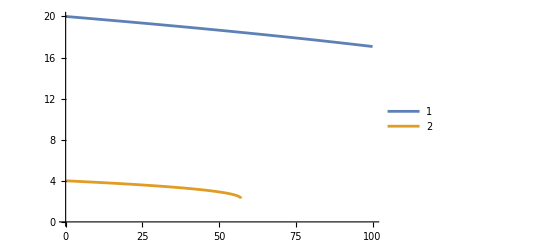

```mathematica
rep={μ->0.1,cq->1,vf->0.005,θ->0,chi->1,e->1};Plot[{(μ+√(μ^2-2 B  Cos[θ] vf^2))/(2 vf)/.rep,(*(μ+√(μ^2-2 B  Cos[θ] vf^2))/(2 vf)-(μ^2 cq)/vf^2/.rep,*)1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))/.rep},{B,0,100},PlotLegends->Automatic]
```

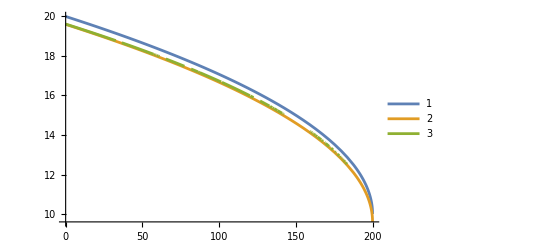

```mathematica
rep={μ->0.1,cq->0.001,vf->0.005,θ->0,chi->1,e->1};Plot[{(μ+√(μ^2-2 B  Cos[θ] vf^2))/(2 vf)/.rep,(μ+√(μ^2-2 B  Cos[θ] vf^2))/(2 vf)-(μ^2 cq)/vf^2/.rep,1/(6 cq)(-2+((-8 vf^3-36 cq vf^2 μ-54 B chi cq^2 e vf^3 Cos[θ]+4 vf^(3/2) √(-4 (vf+3 cq μ)^3+vf (2 vf+9 cq μ+27/2 B chi cq^2 e vf Cos[θ])^2))^(1/3))/vf+(2 2^(2/3) (vf+3 cq μ))/(-18 cq vf^2 μ-vf^3 (4+27 B chi cq^2 e Cos[θ])+3 √3 cq √(vf^3) √(-4 μ^2 (vf+4 cq μ)+B chi e vf^2 Cos[θ] (8 vf+36 cq μ+27 B chi cq^2 e vf Cos[θ])))^(1/3))/.rep},{B,0,200},PlotLegends->Automatic]
```

## phys. quantities for flat band

```mathematica
FullSimplify[Grad[cq vf (kx^2+ky^2+kz^2),{kx,ky,kz}]]
FullSimplify[%.{kx,ky,kz}/.{kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]}]
```

{2 cq kx vf,2 cq ky vf,2 cq kz vf}

2 cq kf^2 vf

```mathematica
Clear[χ,mvec,Bvec,kf,dotprod];
mvec=(-e χ  vf { kx,ky,kz})/(kx^2+ky^2+kz^2) ;
Bvec=B{0,0,1};
Print["omm energy:"];
(*energy corr. from OMM*) dotprod=-mvec.Bvec;
(*energy corr. from OMM*)FullSimplify[dotprod/.{kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]}]
Print["omm velocity:"];
(* vel. from OMM *) FullSimplify[Grad[dotprod,{kx,ky,kz}]];
(* vel. from OMM *) FullSimplify[%/.{kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]}]
```

omm energy:

(B e vf χ Cos[θ])/kf

omm velocity:

{-(B e vf χ Cos[ϕ] Sin[2 θ])/kf^2,-(B e vf χ Sin[2 θ] Sin[ϕ])/kf^2,-(B e vf χ Cos[2 θ])/kf^2}

```mathematica
Bvec=B{0,0,1};mvec=(-e chi  vf { kx,ky,kz})/(2(kx^2+ky^2+kz^2)) ;
vvec=2cq kf{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}vf//FullSimplify;

vomm={-(B chi e vf Cos[ϕ] Sin[2 θ])/kf^2,-(B chi e vf Sin[2 θ] Sin[ϕ])/kf^2,-(B chi e vf Cos[2 θ])/kf^2};

Print["v . k :"];
vdotk= (vf cq kf +vomm.{ Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]})kf//FullSimplify
Print["h0:"];
(* h0 *)FullSimplify[ vvec[[3]]+vomm[[3]]]
```

v . k :

(vf (cq kf^3-B chi e Cos[θ]))/kf

h0:

2 cq kf vf Cos[θ]-(B chi e vf Cos[2 θ])/kf^2

### Fermi surface of flat band

```mathematica
Solve[cq vf kf^2==μ, kf]
```

{{kf→-(√μ)/(√cq √vf)},{kf→(√μ)/(√cq √vf)}}

```mathematica
Clear[rts0,fac];
e=1;chi=1;θ=0;
fac=B e chi Cos[θ];
(*rts0[vf_,cq_,μ_,fac_]=Flatten[FullSimplify[SolveValues[vf kf( cq kf) +vf((*B e chi Cos[θ]*)fac)/kf==μ,kf,Assumptions->ass],Assumptions->ass],1]*)rts0[vf_,cq_,μ_,B_]={((-9 cq^2 fac vf^3+√3 √(cq^3 vf^3 (27 cq fac^2 vf^3-4 μ^3)))^(1/3) (2^(1/3)/(cq vf)+(2 3^(1/3) μ)/((-9 cq^2 fac vf^3+√3 √(cq^3 vf^3 (27 cq fac^2 vf^3-4 μ^3)))^(2/3))))/6^(2/3),((-1)^(1/3) (-9 cq^2 fac vf^3+√3 √(cq^3 vf^3 (27 cq fac^2 vf^3-4 μ^3)))^(1/3) ((-2)^(1/3)/(cq vf)-(2 3^(1/3) μ)/((-9 cq^2 fac vf^3+√3 √(cq^3 vf^3 (27 cq fac^2 vf^3-4 μ^3)))^(2/3))))/6^(2/3),(-((-3 ⅈ+√3) cq vf μ)+(-9 cq^2 fac vf^3+√3 √(cq^3 vf^3 (27 cq fac^2 vf^3-4 μ^3)))^(2/3) Root"-0.757"-"1.31" ⅈRoot[-12+#1^6&,3]-0.7565428747114508)/(2^(2/3) 3^(5/6) cq vf (-9 cq^2 fac vf^3+√3 √(cq^3 vf^3 (27 cq fac^2 vf^3-4 μ^3)))^(1/3))};
Clear[e,chi,θ];
```

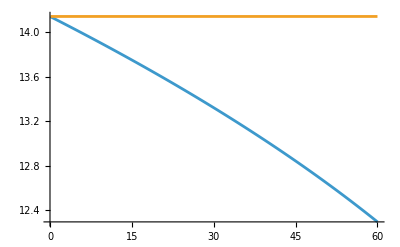

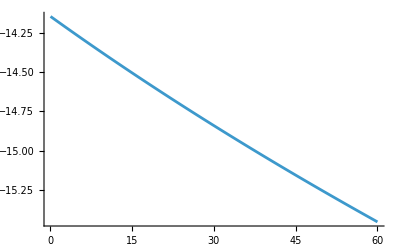

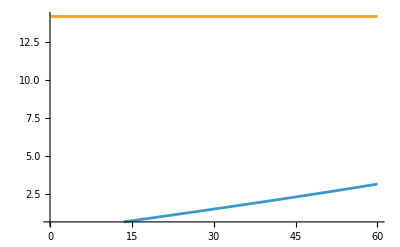

```mathematica
Clear[rt10,rt20,rt30];
vfval=0.005;cqval=0.1;mu=0.1;
{rt10[B_],rt20[B_],rt30[B_]}=rts0[vfval,cqval,mu,B ];
Plot[{rt10[B],(√mu)/(√cqval √vfval)},{B,0.1,60}]
Plot[rt20[B],{B,0.1,60}]
Plot[{rt30[B],(√mu)/(√cqval √vfval)},{B,0.1,60},PlotRange->All]
```

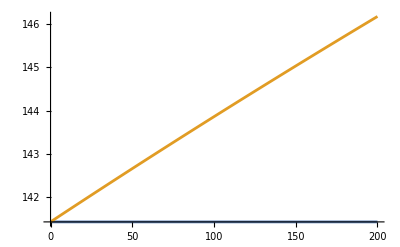

```mathematica
rep={μ->0.1,cq->0.001,vf->0.005,θ->0,chi->-1,e->1}(* nonzero contr regime for linear band *);Plot[{(√μ)/(√cq √vf)/.rep,((-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(1/3) (2^(1/3)/(cq vf)+(2 3^(1/3) μ)/((-9 B chi cq^2 e vf^3 Cos[θ]+√3 √(cq^3 vf^3) √(-4 μ^3+27 B^2 cq e^2 vf^3 Cos[θ]^2))^(2/3))))/6^(2/3)/.rep},{B,0,200}]
```

## Weak field limit

```mathematica
(* from Timm-Meng appendix, for the linear aprrox. bands: -Graphics- *)
(0.1/0.005)^2
```

400.